(l_(1,1) | l_(1,2) | l_(1,3) | l_(1,4) | l_(1,5) | l_(1,6)
l_(2,1) | l_(2,2) | l_(2,3) | l_(2,4) | l_(2,5) | l_(2,6)
l_(3,1) | l_(3,2) | l_(3,3) | l_(3,4) | l_(3,5) | l_(3,6)
l_(4,1) | l_(4,2) | l_(4,3) | l_(4,4) | l_(4,5) | l_(4,6)
l_(5,1) | l_(5,2) | l_(5,3) | l_(5,4) | l_(5,5) | l_(5,6)
l_(6,1) | l_(6,2) | l_(6,3) | l_(6,4) | l_(6,5) | l_(6,6))

{p_1,p_2,p_3,p_4,p_5,p_6}

{d_1,d_2,d_3,d_4,d_5,d_6}

{l_(1,2)+4 l_(1,3)+9 l_(1,4)+16 l_(1,5)+25 l_(1,6)==2 d_1,l_(2,1)+l_(2,3)+4 l_(2,4)+9 l_(2,5)+16 l_(2,6)==2 d_2,4 l_(3,1)+l_(3,2)+l_(3,4)+4 l_(3,5)+9 l_(3,6)==2 d_3,9 l_(4,1)+4 l_(4,2)+l_(4,3)+l_(4,5)+4 l_(4,6)==2 d_4,16 l_(5,1)+9 l_(5,2)+4 l_(5,3)+l_(5,4)+l_(5,6)==2 d_5,l_(1,1)+l_(1,2)+l_(1,3)+l_(1,4)+l_(1,5)+l_(1,6)==0,l_(2,1)+l_(2,2)+l_(2,3)+l_(2,4)+l_(2,5)+l_(2,6)==0,l_(3,1)+l_(3,2)+l_(3,3)+l_(3,4)+l_(3,5)+l_(3,6)==0,l_(4,1)+l_(4,2)+l_(4,3)+l_(4,4)+l_(4,5)+l_(4,6)==0,l_(5,1)+l_(5,2)+l_(5,3)+l_(5,4)+l_(5,5)+l_(5,6)==0,l_(6,1)+l_(6,2)+l_(6,3)+l_(6,4)+l_(6,5)+l_(6,6)==0,l_(2,1)==(p_1 l_(1,2))/p_2,l_(3,1)==(p_1 l_(1,3))/p_3,l_(4,1)==(p_1 l_(1,4))/p_4,l_(5,1)==(p_1 l_(1,5))/p_5,l_(6,1)==(p_1 l_(1,6))/p_6,l_(3,2)==(p_2 l_(2,3))/p_3,l_(4,2)==(p_2 l_(2,4))/p_4,l_(5,2)==(p_2 l_(2,5))/p_5,l_(6,2)==(p_2 l_(2,6))/p_6,l_(4,3)==(p_3 l_(3,4))/p_4,l_(5,3)==(p_3 l_(3,5))/p_5,l_(6,3)==(p_3 l_(3,6))/p_6,l_(5,4)==(p_4 l_(4,5))/p_5,l_(6,4)==(p_4 l_(4,6))/p_6,l_(6,5)==(p_5 l_(5,6))/p_6,l_(1,3)==0,l_(1,4)==0,l_(1,5)==0,l_(1,6)==0,l_(2,4)==0,l_(2,5)==0,l_(2,6)==0,l_(3,5)==0,l_(3,6)==0,l_(4,6)==0}

(-2 d_1 | 2 d_1 | 0 | 0 | 0 | 0
(2 d_1 p_1)/p_2 | -2 d_2 | (2 (-d_1 p_1+d_2 p_2))/p_2 | 0 | 0 | 0
0 | -(2 (d_1 p_1-d_2 p_2))/p_3 | -2 d_3 | (2 (d_1 p_1-d_2 p_2+d_3 p_3))/p_3 | 0 | 0
0 | 0 | (2 (d_1 p_1-d_2 p_2+d_3 p_3))/p_4 | -2 d_4 | (2 (-d_1 p_1+d_2 p_2-d_3 p_3+d_4 p_4))/p_4 | 0
0 | 0 | 0 | -(2 (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4))/p_5 | -2 d_5 | (2 (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4+d_5 p_5))/p_5
0 | 0 | 0 | 0 | (2 (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4+d_5 p_5))/p_6 | -(2 (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4+d_5 p_5))/p_6)

{q_1,q_2,q_3,q_4,q_5,q_6}

{q_1==0,q_6==1,(2 d_1 p_1 q_1)/p_2-2 d_2 q_2+(2 (-d_1 p_1+d_2 p_2) q_3)/p_2==0,-(2 (d_1 p_1-d_2 p_2) q_2)/p_3-2 d_3 q_3+(2 (d_1 p_1-d_2 p_2+d_3 p_3) q_4)/p_3==0,(2 (d_1 p_1-d_2 p_2+d_3 p_3) q_3)/p_4-2 d_4 q_4+(2 (-d_1 p_1+d_2 p_2-d_3 p_3+d_4 p_4) q_5)/p_4==0,-(2 (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4) q_4)/p_5-2 d_5 q_5+(2 (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4+d_5 p_5) q_6)/p_5==0}

qpSol:{0,((-d_1 p_1+d_2 p_2) (-d_1 p_1+d_2 p_2-d_3 p_3) (-d_1 p_1+d_2 p_2-d_3 p_3+d_4 p_4) (-d_1 p_1+d_2 p_2-d_3 p_3+d_4 p_4-d_5 p_5))/(d_1^4 p_1^4-4 d_1^3 d_2 p_1^3 p_2+6 d_1^2 d_2^2 p_1^2 p_2^2-4 d_1 d_2^3 p_1 p_2^3+d_2^4 p_2^4+2 d_1^3 d_3 p_1^3 p_3-7 d_1^2 d_2 d_3 p_1^2 p_2 p_3+8 d_1 d_2^2 d_3 p_1 p_2^2 p_3-3 d_2^3 d_3 p_2^3 p_3+d_1^2 d_3^2 p_1^2 p_3^2-4 d_1 d_2 d_3^2 p_1 p_2 p_3^2+3 d_2^2 d_3^2 p_2^2 p_3^2-d_2 d_3^3 p_2 p_3^3-2 d_1^3 d_4 p_1^3 p_4+6 d_1^2 d_2 d_4 p_1^2 p_2 p_4-6 d_1 d_2^2 d_4 p_1 p_2^2 p_4+2 d_2^3 d_4 p_2^3 p_4-2 d_1^2 d_3 d_4 p_1^2 p_3 p_4+6 d_1 d_2 d_3 d_4 p_1 p_2 p_3 p_4-4 d_2^2 d_3 d_4 p_2^2 p_3 p_4+2 d_2 d_3^2 d_4 p_2 p_3^2 p_4+d_1^2 d_4^2 p_1^2 p_4^2-2 d_1 d_2 d_4^2 p_1 p_2 p_4^2+d_2^2 d_4^2 p_2^2 p_4^2-d_2 d_3 d_4^2 p_2 p_3 p_4^2-d_1^2 d_2 d_5 p_1^2 p_2 p_5+2 d_1 d_2^2 d_5 p_1 p_2^2 p_5-d_2^3 d_5 p_2^3 p_5-2 d_1 d_2 d_3 d_5 p_1 p_2 p_3 p_5+2 d_2^2 d_3 d_5 p_2^2 p_3 p_5-d_2 d_3^2 d_5 p_2 p_3^2 p_5-d_1^2 d_4 d_5 p_1^2 p_4 p_5+2 d_1 d_2 d_4 d_5 p_1 p_2 p_4 p_5-d_2^2 d_4 d_5 p_2^2 p_4 p_5+d_2 d_3 d_4 d_5 p_2 p_3 p_4 p_5),(d_2 p_2 (d_1 p_1-d_2 p_2+d_3 p_3) (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4) (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4+d_5 p_5))/(-d_1^4 p_1^4+4 d_1^3 d_2 p_1^3 p_2-6 d_1^2 d_2^2 p_1^2 p_2^2+4 d_1 d_2^3 p_1 p_2^3-d_2^4 p_2^4-2 d_1^3 d_3 p_1^3 p_3+7 d_1^2 d_2 d_3 p_1^2 p_2 p_3-8 d_1 d_2^2 d_3 p_1 p_2^2 p_3+3 d_2^3 d_3 p_2^3 p_3-d_1^2 d_3^2 p_1^2 p_3^2+4 d_1 d_2 d_3^2 p_1 p_2 p_3^2-3 d_2^2 d_3^2 p_2^2 p_3^2+d_2 d_3^3 p_2 p_3^3+2 d_1^3 d_4 p_1^3 p_4-6 d_1^2 d_2 d_4 p_1^2 p_2 p_4+6 d_1 d_2^2 d_4 p_1 p_2^2 p_4-2 d_2^3 d_4 p_2^3 p_4+2 d_1^2 d_3 d_4 p_1^2 p_3 p_4-6 d_1 d_2 d_3 d_4 p_1 p_2 p_3 p_4+4 d_2^2 d_3 d_4 p_2^2 p_3 p_4-2 d_2 d_3^2 d_4 p_2 p_3^2 p_4-d_1^2 d_4^2 p_1^2 p_4^2+2 d_1 d_2 d_4^2 p_1 p_2 p_4^2-d_2^2 d_4^2 p_2^2 p_4^2+d_2 d_3 d_4^2 p_2 p_3 p_4^2+d_1^2 d_2 d_5 p_1^2 p_2 p_5-2 d_1 d_2^2 d_5 p_1 p_2^2 p_5+d_2^3 d_5 p_2^3 p_5+2 d_1 d_2 d_3 d_5 p_1 p_2 p_3 p_5-2 d_2^2 d_3 d_5 p_2^2 p_3 p_5+d_2 d_3^2 d_5 p_2 p_3^2 p_5+d_1^2 d_4 d_5 p_1^2 p_4 p_5-2 d_1 d_2 d_4 d_5 p_1 p_2 p_4 p_5+d_2^2 d_4 d_5 p_2^2 p_4 p_5-d_2 d_3 d_4 d_5 p_2 p_3 p_4 p_5),((d_1^2 p_1^2-2 d_1 d_2 p_1 p_2+d_2^2 p_2^2-d_2 d_3 p_2 p_3) (-d_1 p_1+d_2 p_2-d_3 p_3+d_4 p_4) (-d_1 p_1+d_2 p_2-d_3 p_3+d_4 p_4-d_5 p_5))/(d_1^4 p_1^4-4 d_1^3 d_2 p_1^3 p_2+6 d_1^2 d_2^2 p_1^2 p_2^2-4 d_1 d_2^3 p_1 p_2^3+d_2^4 p_2^4+2 d_1^3 d_3 p_1^3 p_3-7 d_1^2 d_2 d_3 p_1^2 p_2 p_3+8 d_1 d_2^2 d_3 p_1 p_2^2 p_3-3 d_2^3 d_3 p_2^3 p_3+d_1^2 d_3^2 p_1^2 p_3^2-4 d_1 d_2 d_3^2 p_1 p_2 p_3^2+3 d_2^2 d_3^2 p_2^2 p_3^2-d_2 d_3^3 p_2 p_3^3-2 d_1^3 d_4 p_1^3 p_4+6 d_1^2 d_2 d_4 p_1^2 p_2 p_4-6 d_1 d_2^2 d_4 p_1 p_2^2 p_4+2 d_2^3 d_4 p_2^3 p_4-2 d_1^2 d_3 d_4 p_1^2 p_3 p_4+6 d_1 d_2 d_3 d_4 p_1 p_2 p_3 p_4-4 d_2^2 d_3 d_4 p_2^2 p_3 p_4+2 d_2 d_3^2 d_4 p_2 p_3^2 p_4+d_1^2 d_4^2 p_1^2 p_4^2-2 d_1 d_2 d_4^2 p_1 p_2 p_4^2+d_2^2 d_4^2 p_2^2 p_4^2-d_2 d_3 d_4^2 p_2 p_3 p_4^2-d_1^2 d_2 d_5 p_1^2 p_2 p_5+2 d_1 d_2^2 d_5 p_1 p_2^2 p_5-d_2^3 d_5 p_2^3 p_5-2 d_1 d_2 d_3 d_5 p_1 p_2 p_3 p_5+2 d_2^2 d_3 d_5 p_2^2 p_3 p_5-d_2 d_3^2 d_5 p_2 p_3^2 p_5-d_1^2 d_4 d_5 p_1^2 p_4 p_5+2 d_1 d_2 d_4 d_5 p_1 p_2 p_4 p_5-d_2^2 d_4 d_5 p_2^2 p_4 p_5+d_2 d_3 d_4 d_5 p_2 p_3 p_4 p_5),((d_1^2 d_2 p_1^2 p_2-2 d_1 d_2^2 p_1 p_2^2+d_2^3 p_2^3+2 d_1 d_2 d_3 p_1 p_2 p_3-2 d_2^2 d_3 p_2^2 p_3+d_2 d_3^2 p_2 p_3^2+d_1^2 d_4 p_1^2 p_4-2 d_1 d_2 d_4 p_1 p_2 p_4+d_2^2 d_4 p_2^2 p_4-d_2 d_3 d_4 p_2 p_3 p_4) (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4+d_5 p_5))/(-d_1^4 p_1^4+4 d_1^3 d_2 p_1^3 p_2-6 d_1^2 d_2^2 p_1^2 p_2^2+4 d_1 d_2^3 p_1 p_2^3-d_2^4 p_2^4-2 d_1^3 d_3 p_1^3 p_3+7 d_1^2 d_2 d_3 p_1^2 p_2 p_3-8 d_1 d_2^2 d_3 p_1 p_2^2 p_3+3 d_2^3 d_3 p_2^3 p_3-d_1^2 d_3^2 p_1^2 p_3^2+4 d_1 d_2 d_3^2 p_1 p_2 p_3^2-3 d_2^2 d_3^2 p_2^2 p_3^2+d_2 d_3^3 p_2 p_3^3+2 d_1^3 d_4 p_1^3 p_4-6 d_1^2 d_2 d_4 p_1^2 p_2 p_4+6 d_1 d_2^2 d_4 p_1 p_2^2 p_4-2 d_2^3 d_4 p_2^3 p_4+2 d_1^2 d_3 d_4 p_1^2 p_3 p_4-6 d_1 d_2 d_3 d_4 p_1 p_2 p_3 p_4+4 d_2^2 d_3 d_4 p_2^2 p_3 p_4-2 d_2 d_3^2 d_4 p_2 p_3^2 p_4-d_1^2 d_4^2 p_1^2 p_4^2+2 d_1 d_2 d_4^2 p_1 p_2 p_4^2-d_2^2 d_4^2 p_2^2 p_4^2+d_2 d_3 d_4^2 p_2 p_3 p_4^2+d_1^2 d_2 d_5 p_1^2 p_2 p_5-2 d_1 d_2^2 d_5 p_1 p_2^2 p_5+d_2^3 d_5 p_2^3 p_5+2 d_1 d_2 d_3 d_5 p_1 p_2 p_3 p_5-2 d_2^2 d_3 d_5 p_2^2 p_3 p_5+d_2 d_3^2 d_5 p_2 p_3^2 p_5+d_1^2 d_4 d_5 p_1^2 p_4 p_5-2 d_1 d_2 d_4 d_5 p_1 p_2 p_4 p_5+d_2^2 d_4 d_5 p_2^2 p_4 p_5-d_2 d_3 d_4 d_5 p_2 p_3 p_4 p_5),1}

qpSol-qpMy:{0,1/(d_1 p_1 (1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4)+1/(d_5 p_5)))-((d_1 p_1-d_2 p_2) (d_1 p_1-d_2 p_2+d_3 p_3) (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4) (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4+d_5 p_5))/(d_1^4 p_1^4-2 d_1^3 p_1^3 (2 d_2 p_2-d_3 p_3+d_4 p_4)-2 d_1 d_2 p_1 p_2 (d_2 p_2-d_3 p_3+d_4 p_4) (2 d_2 p_2-2 d_3 p_3+d_4 p_4-d_5 p_5)+d_2 p_2 (d_2 p_2-d_3 p_3) (d_2 p_2-d_3 p_3+d_4 p_4) (d_2 p_2-d_3 p_3+d_4 p_4-d_5 p_5)+d_1^2 p_1^2 (6 d_2^2 p_2^2+d_3^2 p_3^2-2 d_3 d_4 p_3 p_4+d_4 p_4 (d_4 p_4-d_5 p_5)-d_2 p_2 (7 d_3 p_3-6 d_4 p_4+d_5 p_5))),(1/(d_1 p_1)+1/(d_2 p_2))/(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4)+1/(d_5 p_5))-(d_2 p_2 (-d_1 p_1+d_2 p_2-d_3 p_3) (-d_1 p_1+d_2 p_2-d_3 p_3+d_4 p_4) (-d_1 p_1+d_2 p_2-d_3 p_3+d_4 p_4-d_5 p_5))/(d_1^4 p_1^4-2 d_1^3 p_1^3 (2 d_2 p_2-d_3 p_3+d_4 p_4)-2 d_1 d_2 p_1 p_2 (d_2 p_2-d_3 p_3+d_4 p_4) (2 d_2 p_2-2 d_3 p_3+d_4 p_4-d_5 p_5)+d_2 p_2 (d_2 p_2-d_3 p_3) (d_2 p_2-d_3 p_3+d_4 p_4) (d_2 p_2-d_3 p_3+d_4 p_4-d_5 p_5)+d_1^2 p_1^2 (6 d_2^2 p_2^2+d_3^2 p_3^2-2 d_3 d_4 p_3 p_4+d_4 p_4 (d_4 p_4-d_5 p_5)-d_2 p_2 (7 d_3 p_3-6 d_4 p_4+d_5 p_5))),(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3))/(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4)+1/(d_5 p_5))-((d_1^2 p_1^2-2 d_1 d_2 p_1 p_2+d_2 p_2 (d_2 p_2-d_3 p_3)) (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4) (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4+d_5 p_5))/(d_1^4 p_1^4-2 d_1^3 p_1^3 (2 d_2 p_2-d_3 p_3+d_4 p_4)-2 d_1 d_2 p_1 p_2 (d_2 p_2-d_3 p_3+d_4 p_4) (2 d_2 p_2-2 d_3 p_3+d_4 p_4-d_5 p_5)+d_2 p_2 (d_2 p_2-d_3 p_3) (d_2 p_2-d_3 p_3+d_4 p_4) (d_2 p_2-d_3 p_3+d_4 p_4-d_5 p_5)+d_1^2 p_1^2 (6 d_2^2 p_2^2+d_3^2 p_3^2-2 d_3 d_4 p_3 p_4+d_4 p_4 (d_4 p_4-d_5 p_5)-d_2 p_2 (7 d_3 p_3-6 d_4 p_4+d_5 p_5))),(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4))/(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4)+1/(d_5 p_5))+((d_1^2 p_1^2 (d_2 p_2+d_4 p_4)-2 d_1 d_2 p_1 p_2 (d_2 p_2-d_3 p_3+d_4 p_4)+d_2 p_2 (d_2 p_2-d_3 p_3) (d_2 p_2-d_3 p_3+d_4 p_4)) (d_1 p_1-d_2 p_2+d_3 p_3-d_4 p_4+d_5 p_5))/(d_1^4 p_1^4-2 d_1^3 p_1^3 (2 d_2 p_2-d_3 p_3+d_4 p_4)-2 d_1 d_2 p_1 p_2 (d_2 p_2-d_3 p_3+d_4 p_4) (2 d_2 p_2-2 d_3 p_3+d_4 p_4-d_5 p_5)+d_2 p_2 (d_2 p_2-d_3 p_3) (d_2 p_2-d_3 p_3+d_4 p_4) (d_2 p_2-d_3 p_3+d_4 p_4-d_5 p_5)+d_1^2 p_1^2 (6 d_2^2 p_2^2+d_3^2 p_3^2-2 d_3 d_4 p_3 p_4+d_4 p_4 (d_4 p_4-d_5 p_5)-d_2 p_2 (7 d_3 p_3-6 d_4 p_4+d_5 p_5))),0}

kABmy:0.0870871

kAB:0.00180491

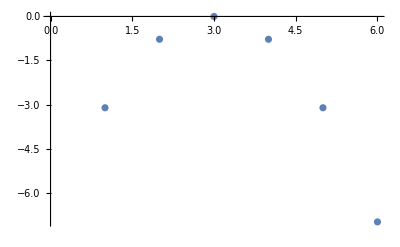

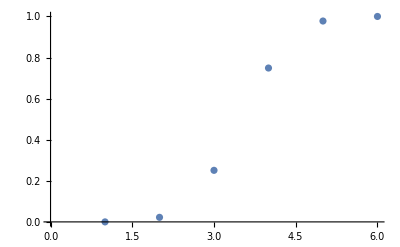

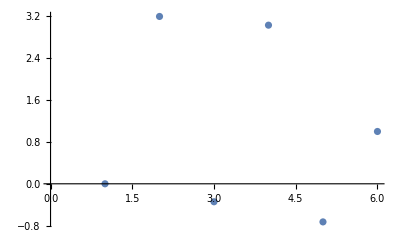

(-d_1 | d_1 | 0 | 0 | 0 | 0
(d_1 p_1)/p_2 | -(d_1 p_1+d_2 p_2)/p_2 | d_2 | 0 | 0 | 0
0 | (d_2 p_2)/p_3 | -d_3-(d_2 p_2)/p_3 | d_3 | 0 | 0
0 | 0 | (d_3 p_3)/p_4 | -d_4-(d_3 p_3)/p_4 | d_4 | 0
0 | 0 | 0 | (d_4 p_4)/p_5 | -d_5-(d_4 p_4)/p_5 | d_5
0 | 0 | 0 | 0 | (d_5 p_5)/p_6 | -(d_5 p_5)/p_6
□ | □ | □ | □ | □ | □)

qpMy:{0,1/(d_1 p_1 (1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4)+1/(d_5 p_5))),(1/(d_1 p_1)+1/(d_2 p_2))/(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4)+1/(d_5 p_5)),(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3))/(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4)+1/(d_5 p_5)),(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4))/(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4)+1/(d_5 p_5)),1}

kABmy:(d_1 d_2 d_3 d_4 d_5 p_1 p_2 p_3 p_4 p_5)/(d_2 d_3 d_4 d_5 p_2 p_3 p_4 p_5+d_1 p_1 (d_3 d_4 d_5 p_3 p_4 p_5+d_2 p_2 (d_3 d_4 p_3 p_4+d_5 (d_3 p_3+d_4 p_4) p_5)))

{q_1,q_2,q_3,q_4,q_5,q_6}

{q_1==0,q_6==1,q_1 l_(2,1)+q_2 l_(2,2)+q_3 l_(2,3)+q_4 l_(2,4)+q_5 l_(2,5)+q_6 l_(2,6)==0,q_1 l_(3,1)+q_2 l_(3,2)+q_3 l_(3,3)+q_4 l_(3,4)+q_5 l_(3,5)+q_6 l_(3,6)==0,q_1 l_(4,1)+q_2 l_(4,2)+q_3 l_(4,3)+q_4 l_(4,4)+q_5 l_(4,5)+q_6 l_(4,6)==0,q_1 l_(5,1)+q_2 l_(5,2)+q_3 l_(5,3)+q_4 l_(5,4)+q_5 l_(5,5)+q_6 l_(5,6)==0}

qpDiff:{0,1/(d_1 p_1 (1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4)+1/(d_5 p_5)))+(-l_(2,4) l_(3,6) l_(4,5) l_(5,3)+l_(2,4) l_(3,5) l_(4,6) l_(5,3)+l_(2,3) l_(3,6) l_(4,5) l_(5,4)-l_(2,3) l_(3,5) l_(4,6) l_(5,4)+l_(2,4) l_(3,6) l_(4,3) l_(5,5)-l_(2,3) l_(3,6) l_(4,4) l_(5,5)-l_(2,4) l_(3,3) l_(4,6) l_(5,5)+l_(2,3) l_(3,4) l_(4,6) l_(5,5)+l_(2,6) (l_(3,5) (-l_(4,4) l_(5,3)+l_(4,3) l_(5,4))+l_(3,4) (l_(4,5) l_(5,3)-l_(4,3) l_(5,5))+l_(3,3) (-l_(4,5) l_(5,4)+l_(4,4) l_(5,5)))-l_(2,4) l_(3,5) l_(4,3) l_(5,6)+l_(2,3) l_(3,5) l_(4,4) l_(5,6)+l_(2,4) l_(3,3) l_(4,5) l_(5,6)-l_(2,3) l_(3,4) l_(4,5) l_(5,6)+l_(2,5) (l_(3,6) (l_(4,4) l_(5,3)-l_(4,3) l_(5,4))+l_(3,4) (-l_(4,6) l_(5,3)+l_(4,3) l_(5,6))+l_(3,3) (l_(4,6) l_(5,4)-l_(4,4) l_(5,6))))/(l_(2,3) l_(3,5) l_(4,4) l_(5,2)-l_(2,3) l_(3,4) l_(4,5) l_(5,2)-l_(2,2) l_(3,5) l_(4,4) l_(5,3)+l_(2,2) l_(3,4) l_(4,5) l_(5,3)-l_(2,3) l_(3,5) l_(4,2) l_(5,4)+l_(2,2) l_(3,5) l_(4,3) l_(5,4)+l_(2,3) l_(3,2) l_(4,5) l_(5,4)-l_(2,2) l_(3,3) l_(4,5) l_(5,4)+l_(2,5) (l_(3,4) (l_(4,3) l_(5,2)-l_(4,2) l_(5,3))+l_(3,3) (-l_(4,4) l_(5,2)+l_(4,2) l_(5,4))+l_(3,2) (l_(4,4) l_(5,3)-l_(4,3) l_(5,4)))+l_(2,3) l_(3,4) l_(4,2) l_(5,5)-l_(2,2) l_(3,4) l_(4,3) l_(5,5)-l_(2,3) l_(3,2) l_(4,4) l_(5,5)+l_(2,2) l_(3,3) l_(4,4) l_(5,5)+l_(2,4) (l_(3,5) (-l_(4,3) l_(5,2)+l_(4,2) l_(5,3))+l_(3,3) (l_(4,5) l_(5,2)-l_(4,2) l_(5,5))+l_(3,2) (-l_(4,5) l_(5,3)+l_(4,3) l_(5,5)))),(1/(d_1 p_1)+1/(d_2 p_2))/(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4)+1/(d_5 p_5))+(l_(2,4) l_(3,6) l_(4,5) l_(5,2)-l_(2,4) l_(3,5) l_(4,6) l_(5,2)-l_(2,2) l_(3,6) l_(4,5) l_(5,4)+l_(2,2) l_(3,5) l_(4,6) l_(5,4)-l_(2,4) l_(3,6) l_(4,2) l_(5,5)+l_(2,2) l_(3,6) l_(4,4) l_(5,5)+l_(2,4) l_(3,2) l_(4,6) l_(5,5)-l_(2,2) l_(3,4) l_(4,6) l_(5,5)+l_(2,6) (l_(3,5) (l_(4,4) l_(5,2)-l_(4,2) l_(5,4))+l_(3,4) (-l_(4,5) l_(5,2)+l_(4,2) l_(5,5))+l_(3,2) (l_(4,5) l_(5,4)-l_(4,4) l_(5,5)))+l_(2,4) l_(3,5) l_(4,2) l_(5,6)-l_(2,2) l_(3,5) l_(4,4) l_(5,6)-l_(2,4) l_(3,2) l_(4,5) l_(5,6)+l_(2,2) l_(3,4) l_(4,5) l_(5,6)+l_(2,5) (l_(3,6) (-l_(4,4) l_(5,2)+l_(4,2) l_(5,4))+l_(3,4) (l_(4,6) l_(5,2)-l_(4,2) l_(5,6))+l_(3,2) (-l_(4,6) l_(5,4)+l_(4,4) l_(5,6))))/(l_(2,3) l_(3,5) l_(4,4) l_(5,2)-l_(2,3) l_(3,4) l_(4,5) l_(5,2)-l_(2,2) l_(3,5) l_(4,4) l_(5,3)+l_(2,2) l_(3,4) l_(4,5) l_(5,3)-l_(2,3) l_(3,5) l_(4,2) l_(5,4)+l_(2,2) l_(3,5) l_(4,3) l_(5,4)+l_(2,3) l_(3,2) l_(4,5) l_(5,4)-l_(2,2) l_(3,3) l_(4,5) l_(5,4)+l_(2,5) (l_(3,4) (l_(4,3) l_(5,2)-l_(4,2) l_(5,3))+l_(3,3) (-l_(4,4) l_(5,2)+l_(4,2) l_(5,4))+l_(3,2) (l_(4,4) l_(5,3)-l_(4,3) l_(5,4)))+l_(2,3) l_(3,4) l_(4,2) l_(5,5)-l_(2,2) l_(3,4) l_(4,3) l_(5,5)-l_(2,3) l_(3,2) l_(4,4) l_(5,5)+l_(2,2) l_(3,3) l_(4,4) l_(5,5)+l_(2,4) (l_(3,5) (-l_(4,3) l_(5,2)+l_(4,2) l_(5,3))+l_(3,3) (l_(4,5) l_(5,2)-l_(4,2) l_(5,5))+l_(3,2) (-l_(4,5) l_(5,3)+l_(4,3) l_(5,5)))),(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3))/(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4)+1/(d_5 p_5))+(-l_(2,3) l_(3,6) l_(4,5) l_(5,2)+l_(2,3) l_(3,5) l_(4,6) l_(5,2)+l_(2,2) l_(3,6) l_(4,5) l_(5,3)-l_(2,2) l_(3,5) l_(4,6) l_(5,3)+l_(2,3) l_(3,6) l_(4,2) l_(5,5)-l_(2,2) l_(3,6) l_(4,3) l_(5,5)-l_(2,3) l_(3,2) l_(4,6) l_(5,5)+l_(2,2) l_(3,3) l_(4,6) l_(5,5)+l_(2,6) (l_(3,5) (-l_(4,3) l_(5,2)+l_(4,2) l_(5,3))+l_(3,3) (l_(4,5) l_(5,2)-l_(4,2) l_(5,5))+l_(3,2) (-l_(4,5) l_(5,3)+l_(4,3) l_(5,5)))-l_(2,3) l_(3,5) l_(4,2) l_(5,6)+l_(2,2) l_(3,5) l_(4,3) l_(5,6)+l_(2,3) l_(3,2) l_(4,5) l_(5,6)-l_(2,2) l_(3,3) l_(4,5) l_(5,6)+l_(2,5) (l_(3,6) (l_(4,3) l_(5,2)-l_(4,2) l_(5,3))+l_(3,3) (-l_(4,6) l_(5,2)+l_(4,2) l_(5,6))+l_(3,2) (l_(4,6) l_(5,3)-l_(4,3) l_(5,6))))/(l_(2,3) l_(3,5) l_(4,4) l_(5,2)-l_(2,3) l_(3,4) l_(4,5) l_(5,2)-l_(2,2) l_(3,5) l_(4,4) l_(5,3)+l_(2,2) l_(3,4) l_(4,5) l_(5,3)-l_(2,3) l_(3,5) l_(4,2) l_(5,4)+l_(2,2) l_(3,5) l_(4,3) l_(5,4)+l_(2,3) l_(3,2) l_(4,5) l_(5,4)-l_(2,2) l_(3,3) l_(4,5) l_(5,4)+l_(2,5) (l_(3,4) (l_(4,3) l_(5,2)-l_(4,2) l_(5,3))+l_(3,3) (-l_(4,4) l_(5,2)+l_(4,2) l_(5,4))+l_(3,2) (l_(4,4) l_(5,3)-l_(4,3) l_(5,4)))+l_(2,3) l_(3,4) l_(4,2) l_(5,5)-l_(2,2) l_(3,4) l_(4,3) l_(5,5)-l_(2,3) l_(3,2) l_(4,4) l_(5,5)+l_(2,2) l_(3,3) l_(4,4) l_(5,5)+l_(2,4) (l_(3,5) (-l_(4,3) l_(5,2)+l_(4,2) l_(5,3))+l_(3,3) (l_(4,5) l_(5,2)-l_(4,2) l_(5,5))+l_(3,2) (-l_(4,5) l_(5,3)+l_(4,3) l_(5,5)))),(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4))/(1/(d_1 p_1)+1/(d_2 p_2)+1/(d_3 p_3)+1/(d_4 p_4)+1/(d_5 p_5))+(l_(2,3) l_(3,6) l_(4,4) l_(5,2)-l_(2,3) l_(3,4) l_(4,6) l_(5,2)-l_(2,2) l_(3,6) l_(4,4) l_(5,3)+l_(2,2) l_(3,4) l_(4,6) l_(5,3)-l_(2,3) l_(3,6) l_(4,2) l_(5,4)+l_(2,2) l_(3,6) l_(4,3) l_(5,4)+l_(2,3) l_(3,2) l_(4,6) l_(5,4)-l_(2,2) l_(3,3) l_(4,6) l_(5,4)+l_(2,6) (l_(3,4) (l_(4,3) l_(5,2)-l_(4,2) l_(5,3))+l_(3,3) (-l_(4,4) l_(5,2)+l_(4,2) l_(5,4))+l_(3,2) (l_(4,4) l_(5,3)-l_(4,3) l_(5,4)))+l_(2,3) l_(3,4) l_(4,2) l_(5,6)-l_(2,2) l_(3,4) l_(4,3) l_(5,6)-l_(2,3) l_(3,2) l_(4,4) l_(5,6)+l_(2,2) l_(3,3) l_(4,4) l_(5,6)+l_(2,4) (l_(3,6) (-l_(4,3) l_(5,2)+l_(4,2) l_(5,3))+l_(3,3) (l_(4,6) l_(5,2)-l_(4,2) l_(5,6))+l_(3,2) (-l_(4,6) l_(5,3)+l_(4,3) l_(5,6))))/(l_(2,3) l_(3,5) l_(4,4) l_(5,2)-l_(2,3) l_(3,4) l_(4,5) l_(5,2)-l_(2,2) l_(3,5) l_(4,4) l_(5,3)+l_(2,2) l_(3,4) l_(4,5) l_(5,3)-l_(2,3) l_(3,5) l_(4,2) l_(5,4)+l_(2,2) l_(3,5) l_(4,3) l_(5,4)+l_(2,3) l_(3,2) l_(4,5) l_(5,4)-l_(2,2) l_(3,3) l_(4,5) l_(5,4)+l_(2,5) (l_(3,4) (l_(4,3) l_(5,2)-l_(4,2) l_(5,3))+l_(3,3) (-l_(4,4) l_(5,2)+l_(4,2) l_(5,4))+l_(3,2) (l_(4,4) l_(5,3)-l_(4,3) l_(5,4)))+l_(2,3) l_(3,4) l_(4,2) l_(5,5)-l_(2,2) l_(3,4) l_(4,3) l_(5,5)-l_(2,3) l_(3,2) l_(4,4) l_(5,5)+l_(2,2) l_(3,3) l_(4,4) l_(5,5)+l_(2,4) (l_(3,5) (-l_(4,3) l_(5,2)+l_(4,2) l_(5,3))+l_(3,3) (l_(4,5) l_(5,2)-l_(4,2) l_(5,5))+l_(3,2) (-l_(4,5) l_(5,3)+l_(4,3) l_(5,5)))),0}

kAB:d_5 p_5 (1+(l_(2,6) l_(3,4) l_(4,3) l_(5,2)-l_(2,4) l_(3,6) l_(4,3) l_(5,2)-l_(2,6) l_(3,3) l_(4,4) l_(5,2)+l_(2,3) l_(3,6) l_(4,4) l_(5,2)+l_(2,4) l_(3,3) l_(4,6) l_(5,2)-l_(2,3) l_(3,4) l_(4,6) l_(5,2)-l_(2,6) l_(3,4) l_(4,2) l_(5,3)+l_(2,4) l_(3,6) l_(4,2) l_(5,3)+l_(2,6) l_(3,2) l_(4,4) l_(5,3)-l_(2,2) l_(3,6) l_(4,4) l_(5,3)-l_(2,4) l_(3,2) l_(4,6) l_(5,3)+l_(2,2) l_(3,4) l_(4,6) l_(5,3)+l_(2,6) l_(3,3) l_(4,2) l_(5,4)-l_(2,3) l_(3,6) l_(4,2) l_(5,4)-l_(2,6) l_(3,2) l_(4,3) l_(5,4)+l_(2,2) l_(3,6) l_(4,3) l_(5,4)+l_(2,3) l_(3,2) l_(4,6) l_(5,4)-l_(2,2) l_(3,3) l_(4,6) l_(5,4)-l_(2,4) l_(3,3) l_(4,2) l_(5,6)+l_(2,3) l_(3,4) l_(4,2) l_(5,6)+l_(2,4) l_(3,2) l_(4,3) l_(5,6)-l_(2,2) l_(3,4) l_(4,3) l_(5,6)-l_(2,3) l_(3,2) l_(4,4) l_(5,6)+l_(2,2) l_(3,3) l_(4,4) l_(5,6))/(l_(2,5) l_(3,4) l_(4,3) l_(5,2)-l_(2,4) l_(3,5) l_(4,3) l_(5,2)-l_(2,5) l_(3,3) l_(4,4) l_(5,2)+l_(2,3) l_(3,5) l_(4,4) l_(5,2)+l_(2,4) l_(3,3) l_(4,5) l_(5,2)-l_(2,3) l_(3,4) l_(4,5) l_(5,2)-l_(2,5) l_(3,4) l_(4,2) l_(5,3)+l_(2,4) l_(3,5) l_(4,2) l_(5,3)+l_(2,5) l_(3,2) l_(4,4) l_(5,3)-l_(2,2) l_(3,5) l_(4,4) l_(5,3)-l_(2,4) l_(3,2) l_(4,5) l_(5,3)+l_(2,2) l_(3,4) l_(4,5) l_(5,3)+l_(2,5) l_(3,3) l_(4,2) l_(5,4)-l_(2,3) l_(3,5) l_(4,2) l_(5,4)-l_(2,5) l_(3,2) l_(4,3) l_(5,4)+l_(2,2) l_(3,5) l_(4,3) l_(5,4)+l_(2,3) l_(3,2) l_(4,5) l_(5,4)-l_(2,2) l_(3,3) l_(4,5) l_(5,4)-l_(2,4) l_(3,3) l_(4,2) l_(5,5)+l_(2,3) l_(3,4) l_(4,2) l_(5,5)+l_(2,4) l_(3,2) l_(4,3) l_(5,5)-l_(2,2) l_(3,4) l_(4,3) l_(5,5)-l_(2,3) l_(3,2) l_(4,4) l_(5,5)+l_(2,2) l_(3,3) l_(4,4) l_(5,5)))

d_5 p_5 (1+(l_(2,3) l_(3,6) l_(4,4) l_(5,2)-l_(2,3) l_(3,4) l_(4,6) l_(5,2)-l_(2,2) l_(3,6) l_(4,4) l_(5,3)+l_(2,2) l_(3,4) l_(4,6) l_(5,3)-l_(2,3) l_(3,6) l_(4,2) l_(5,4)+l_(2,2) l_(3,6) l_(4,3) l_(5,4)+l_(2,3) l_(3,2) l_(4,6) l_(5,4)-l_(2,2) l_(3,3) l_(4,6) l_(5,4)+l_(2,6) (l_(3,4) (l_(4,3) l_(5,2)-l_(4,2) l_(5,3))+l_(3,3) (-l_(4,4) l_(5,2)+l_(4,2) l_(5,4))+l_(3,2) (l_(4,4) l_(5,3)-l_(4,3) l_(5,4)))+l_(2,3) l_(3,4) l_(4,2) l_(5,6)-l_(2,2) l_(3,4) l_(4,3) l_(5,6)-l_(2,3) l_(3,2) l_(4,4) l_(5,6)+l_(2,2) l_(3,3) l_(4,4) l_(5,6)+l_(2,4) (l_(3,6) (-l_(4,3) l_(5,2)+l_(4,2) l_(5,3))+l_(3,3) (l_(4,6) l_(5,2)-l_(4,2) l_(5,6))+l_(3,2) (-l_(4,6) l_(5,3)+l_(4,3) l_(5,6))))/(l_(2,3) l_(3,5) l_(4,4) l_(5,2)-l_(2,3) l_(3,4) l_(4,5) l_(5,2)-l_(2,2) l_(3,5) l_(4,4) l_(5,3)+l_(2,2) l_(3,4) l_(4,5) l_(5,3)-l_(2,3) l_(3,5) l_(4,2) l_(5,4)+l_(2,2) l_(3,5) l_(4,3) l_(5,4)+l_(2,3) l_(3,2) l_(4,5) l_(5,4)-l_(2,2) l_(3,3) l_(4,5) l_(5,4)+l_(2,5) (l_(3,4) (l_(4,3) l_(5,2)-l_(4,2) l_(5,3))+l_(3,3) (-l_(4,4) l_(5,2)+l_(4,2) l_(5,4))+l_(3,2) (l_(4,4) l_(5,3)-l_(4,3) l_(5,4)))+l_(2,3) l_(3,4) l_(4,2) l_(5,5)-l_(2,2) l_(3,4) l_(4,3) l_(5,5)-l_(2,3) l_(3,2) l_(4,4) l_(5,5)+l_(2,2) l_(3,3) l_(4,4) l_(5,5)+l_(2,4) (l_(3,5) (-l_(4,3) l_(5,2)+l_(4,2) l_(5,3))+l_(3,3) (l_(4,5) l_(5,2)-l_(4,2) l_(5,5))+l_(3,2) (-l_(4,5) l_(5,3)+l_(4,3) l_(5,5)))))

0.0445918

-Graphics-

-Graphics-

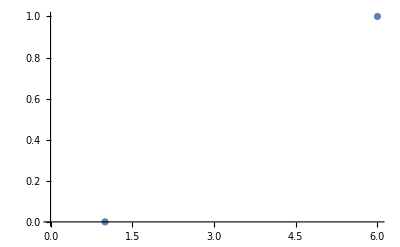

```mathematica
ClearAll[n,lMat,piVec,dVec,localJumps,localJumps2,detailedBalance,probConserv,diffusionRates,diffusionRates1,diffusionRates2,diffusionRates3,eqs,eqsNoD,sol,lSolved,qpZ,qpMyVec,kAB,kABcnt,kABmy,dFA,fNum,pNum,dNum,numSubst,l,p,d,q,i,j];
n=6;
lMat = Table[Subscript[l,i,j],{i,n},{j,n}];
Print[lMat//MatrixForm];
piVec = Table[Subscript[p,i],{i,n}];
dVec = Table[Subscript[d,i],{i,n}];
Print[piVec]
Print[dVec]
probConserv=Table[Sum[lMat[[i,j]],{j,1,n}]==0,{i,1,n}];
detailedBalance=Flatten[Table[Table[lMat[[j,i]]==lMat[[i,j]]*piVec[[i]]/piVec[[j]],{j,i+1,n}],{i,1,n-1}]];
localJumps=Flatten[Table[Table[lMat[[i,j]]==0,{j,i+2,n}],{i,1,n-2}]];
localJumps2=Flatten[Table[Table[lMat[[i,j]]==0,{j,i+2,n}],{i,1,n-3}]];
diffusionRates2=Table[Sum[lMat[[i,j]]*(i-j)^2,{j,1,n}]==2*dVec[[i]],{i,1,n-1}];
diffusionRates3=Table[lMat[[i,i+1]]==dVec[[i]],{i,1,n-1}];
eqs=Join[diffusionRates2,probConserv,detailedBalance,localJumps];
(*eqsNoD=Join[diffusionRates3,probConserv,detailedBalance,localJumps];*)
Print[eqs]
lVec=Flatten[lMat];
sol=Solve[eqs,lVec];
lSolved=lMat/.sol[[1]];
Print[lSolved//MatrixForm];
qpZ=Sum[1/(piVec[[i]]*dVec[[i]]),{i,1,n-1}];
qpMyVec=Table[Sum[1/(piVec[[j]]*dVec[[j]]),{j,1,i-1}]/qpZ,{i,1,n}];
(*Print["qpMy:",qpMyVec];*)
kABmy=piVec[[n-1]]*lSolved[[n-1,n]]*(1-qpMyVec[[n-1]]);
(*Print["kABmy:",FullSimplify[kABmy]];*)

qpVec=Table[Subscript[q,i],{i,1,n}];
qEqs=Join[{qpVec[[1]]==0,qpVec[[n]]==1},Table[Sum[qpVec[[j]]*lSolved[[i,j]],{j,1,n}]==0,{i,2,n-1}]];
Print[qpVec];
Print[qEqs];
qpSol=Solve[qEqs,qpVec];
qpSolved=qpVec/.qpSol[[1]];
Print["qpSol:",qpSolved];
(*Print["qpDiff:",Table[qpMyVec[[i]]-qpSolved[[i]],{i,1,n}]];*)
Print["qpSol-qpMy:",Table[Simplify[qpMyVec[[i]]-qpSolved[[i]]],{i,1,n}]];
kAB=1/Sum[1/piVec[[j]]*lSolved[[j,j+1]],{j,1,n-1}];
(*Print["kAB:",kAB];*)
(*Print[Simplify[kAB]];*)

dFA=7.0;

fNum=Table[-dFA*((2*i/n-1))^2,{i,1,n}];
pNum=Table[piVec[[i]]->Exp[-fNum[[i]]]/Sum[Exp[-fNum[[j]]],{j,1,n}],{i,1,n}];
dNum=Table[dVec[[i]]->1.0,{i,1,n}];
numSubst=Flatten[Join[pNum,dNum]];
kABcnt=(Sqrt[dFA/(Pi)]*2/n)*((lSolved[[Round[n/2],Round[n/2]+1]]/.numSubst))*Exp[-Max[fNum]]/Sum[Exp[-fNum[[i]]],{i,1,n}];

Print["kABmy:",(kABmy/.numSubst)/kABcnt];
Print["kAB:",(kAB/.numSubst)/kABcnt];

ListPlot[fNum]
ListPlot[qpMyVec/.numSubst]
ListPlot[qpSolved/.numSubst]
```

```mathematica
n=5;
Round[n/2]
```

2